### Basic:

```mathematica
FNJ=FileNameJoin;
```

```mathematica
RelativeDir[dir_]:=FileNameJoin[{NotebookDirectory[],dir}]
```

```mathematica
Replicate[list_,n_]:=Flatten[Transpose[ConstantArray[list,n]]]
```

```mathematica
ToText[list_]:=StringJoin[Riffle[ToString[#]&/@list,"\n"]]
```

```mathematica
ShiftLeft[list_,n_]:=Drop[PadLeft[list,Length[list]+n],-n]
```

```mathematica
ShiftRight[list_,n_]:=Drop[PadRight[list,Length[list]+n],n]
```

### Before simulation:

```mathematica
(*-------parameters-------*)
td = 8; blocks = 4; l = 100;
(*------------------------*)
data=RandomInteger[{-16,16},l];
ker = RandomInteger[{-16,16},td*blocks];
```

```mathematica
expected=ListConvolve[Reverse[ker],data,{1,-1},0];
```

```mathematica
Max[Abs[expected]]
```

1062

```mathematica
Export[RelativeDir["data.dat"],ToText[Replicate[data,td]]];Export[RelativeDir["coefs.dat"],ToText[ker]];
```

### After simulation:

```mathematica
result=Flatten[Import[RelativeDir[FNJ[{"edit_firIP_v1_0.sim","sim_1","behav","xsim","out.dat"}]]]];
```

```mathematica
SequencePosition[result,Replicate[expected,td]]
```

{}

### Random:

```mathematica
2224189. /2^16
```

33.9384

### Samples from fpga:

```mathematica
2^14
```

16384

```mathematica
85*6229+960
```

530425

```mathematica
snaps=Reverse/@Import[RelativeDir["snap10.dat"]];
registers = {"fir_in","sum_loop_out", "sum_loop_end", "count","x","coef_crr","sum_in","sum_out"};
```

```mathematica
firIn=Downsample[snaps[[1]],2,1]; firOut = Downsample[snaps[[2]],2,2];
```

```mathematica
BitShiftRight[firOut,16]
```

{-808,-870,-773,-536,-207,148,459,661,715,609,366,34,-319,-625,-822,-869,-757,-509,-174,179,481,670,708,588,334,-2,-354,-651,-833,-864,-737,-478,-137,214,507,682,705,570,305,-35,-385,-673,-841,-857,-715,-445,-100,248,532,693}

```mathematica
firOutS=Downsample[snaps[[3]],2]
```

{-600,-809,-871,-774,-537,-208,148,459,661,715,609,366,34,-320,-626,-823,-870,-758,-510,-175,179,481,670,708,588,334,-3,-355,-652,-834,-865,-738,-479,-138,214,507,682,705,570,305,-36,-386,-674,-842,-858,-716,-446,-101,248,532}

```mathematica
ker={52,150,393,872,1630,2633,3770,4871,5745,6229,6229,5745,4871,3770,2633,1630,872,393,150,52}
```

{52,150,393,872,1630,2633,3770,4871,5745,6229,6229,5745,4871,3770,2633,1630,872,393,150,52}

```mathematica
ListConvolve[ker,firIn]
```

{14054772,33267127,44745189,46204290,37371889,20031992,-2340782,-25259741,-44131255,-55174024,-56167359,-46891360,-29184679,-6604508,16292402,34880765,45424627,45823061,36013029,17970542,-4690099,-27426384,-45682845,-55802274,-55750681,-45520180,-27146941,-4329981,18318687,36221815,45779846}

```mathematica
firOut
```

{-52957126,-57045866,-50703626,-35175093,-13569241,9758538,30096254,43349108,46869436,39968431,24041994,2279233,-20959773,-41020978,-53889101,-56984195,-49673534,-33403820,-11441120,11783828,31578304,43958256,46453047,38580780,21933273,-151579,-23242434,-42710790,-54654944,-56677116,-48354338,-31333836,-9031638,14054772,33267127,44745189,46204290,37371889,20031992,-2340782,-25259741,-44131255,-55174024,-56167359,-46891360,-29184679,-6604508,16292402,34880765,45424627}

```mathematica
LongestCommonSubsequence[ListConvolve[ker,firIn],firOut]
```

{14054772,33267127,44745189,46204290,37371889,20031992,-2340782,-25259741,-44131255,-55174024,-56167359,-46891360,-29184679,-6604508,16292402,34880765,45424627}

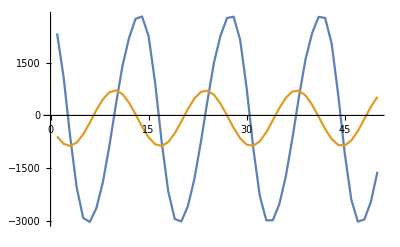

```mathematica
ListPlot[{firIn,firOutS},Joined->True]
```

```mathematica
TableForm[Join[{Range[Length[snaps]]},Transpose@snaps]];
```

```mathematica
rng=Range[#,#+3]&/@Range[1,5*3,3];
```

```mathematica
(*(Drop[ShiftRight[snaps[[#1]],1]+(snaps[[#2]]*snaps[[#3]]),-4]==Drop[snaps[[#4]],4])&@@@rng*)
```

### Upsampling:

```mathematica
upker={0.004349354184333842,-0.012460526975242473,-0.04179305187785534,0.11580155515788863,0.4377645703903624,0.4377645703903624,0.11580155515788867,-0.04179305187785537,-0.012460526975242473,0.004349354184333842};
```

```mathematica
f=0.113;
```

```mathematica
in=Sin[2*π*f*#]&/@Range[100];
```

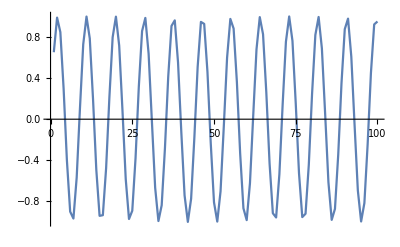

```mathematica
ListPlot[in,Joined->True]
```

```mathematica
inR=Riffle[in,0];
```

```mathematica
out=ListConvolve[upker,inR,1,0];
```

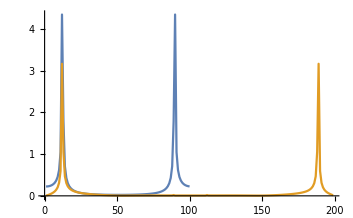

```mathematica
ListPlot[{Abs[Fourier[in]],Abs[Fourier[out]]},Joined->True,PlotRange->All]
```

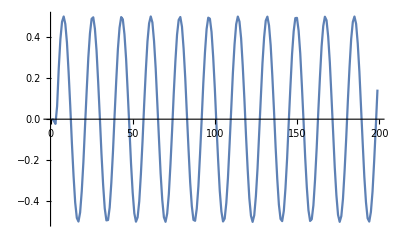

```mathematica
ListPlot[out,Joined->True]
```